# RMT

```mathematica
Get["QMB`"]
```

## LevelSpacingDistribution

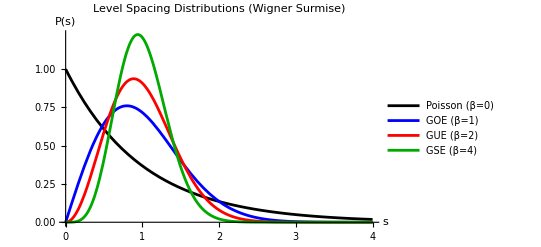

1

1

```mathematica
(* 1. Visualización de la transición del Caos Cuántico *)
(* Compara sistemas integrables (Poisson) con repulsión de niveles (Wigner-Dyson) *)
Plot[{
    LevelSpacingDistribution[s, 0], 
    LevelSpacingDistribution[s, 1], 
    LevelSpacingDistribution[s, 2],
    LevelSpacingDistribution[s, 4]
}, {s, 0, 4},
    PlotLegends -> {"Poisson (β=0)", "GOE (β=1)", "GUE (β=2)", "GSE (β=4)"},
    PlotStyle -> {Black, Blue, Red, Darker[Green]},
    AxesLabel -> {"s", "P(s)"},
    PlotRange -> All,
    PlotLabel -> "Level Spacing Distributions (Wigner Surmise)"
]

(* 2. Verificación Analítica Estricta: Normalización de Probabilidad \int P(s) ds = 1 *)
Integrate[LevelSpacingDistribution[s, 1], {s, 0, Infinity}]

(* 3. Verificación Analítica Estricta: Normalización de la media \int s P(s) ds = 1 *)
Integrate[s * LevelSpacingDistribution[s, 2], {s, 0, Infinity}]

(* 4. Aplicación usando EmpiricalKLDivergence ya existente en tu paquete QMB *)
(*
  UnfoldedSpacings = Differences[Unfold[NumericalSpectrum]["UnfoldedLevels"]];
  KLDistanceToGOE = EmpiricalKLDivergence[UnfoldedSpacings, LevelSpacingDistribution[#, 1]&];
*)
```